```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/inhomo/MF_DR/spec/sub_renormalization/mu250T100

```mathematica
Re1=Import["./RedataT100mu250v2.dat"];
Im1=Import["./ImdataT100mu250.dat"];
Re2=Re1;
Im2=Im1;
spec=-1/π*Im2/(Re2^2+Im2^2);
```

```mathematica
ListPlot3D[spec,PlotRange->{All,All,{0,0.000001}}]
```

-Graphics3D-

```mathematica
special=Clip[spec,{0,0.0000015}];
```

```mathematica
ListPlot3D[special]
```

-Graphics3D-

```mathematica
Export["spec.dat",special]
```

spec.dat

```mathematica
ListPlot3D[Re1]
```

-Graphics3D-

```mathematica
ListPlot3D[-Im1]
```

-Graphics3D-

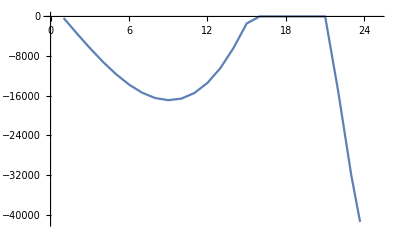

```mathematica
ListLinePlot[Im1[[30]][[1;;25]]]
```